#### 3 aneis simples

```mathematica
Ω=({{Δ, κ, 0}, {κ, Δ, κ}, {0, κ, Δ}}); a=({{a0}, {a1}, {a2}}); K=({{I μ1, 0, 0}}); Γ = Γi + Γe; Γi = ({{μ1^2/2, 0, 0}, {0, μ1^2/2, 0}, {0, 0, μ1^2/2}}); Γe = ({{μ1^2/2, 0, 0}, {0, 0, 0}, {0, 0, 0}});Cmatrix=1;
```

```mathematica
dadt = (I Ω - Γ).a + Transpose[K] sin//MatrixForm
```

(ⅈ a1 κ+ⅈ sin μ1+a0 (ⅈ Δ-μ1^2)
ⅈ a0 κ+ⅈ a2 κ+a1 (ⅈ Δ-μ1^2/2)
ⅈ a1 κ+a2 (ⅈ Δ-μ1^2/2))

```mathematica
Solve[dadt[[1,1]]==0 && dadt[[1,2]]==0&& dadt[[1,3]]==0 , {a0,a1,a2}]
```

{{a0→(ⅈ sin μ1 (-4 Δ^2+4 κ^2-4 ⅈ Δ μ1^2+μ1^4))/(4 ⅈ Δ^3-8 ⅈ Δ κ^2-8 Δ^2 μ1^2+6 κ^2 μ1^2-5 ⅈ Δ μ1^4+μ1^6),a1→-(2 sin κ μ1 (-2 ⅈ Δ+μ1^2))/(4 ⅈ Δ^3-8 ⅈ Δ κ^2-8 Δ^2 μ1^2+6 κ^2 μ1^2-5 ⅈ Δ μ1^4+μ1^6),a2→(4 sin κ^2 μ1)/(-4 Δ^3+8 Δ κ^2-8 ⅈ Δ^2 μ1^2+6 ⅈ κ^2 μ1^2+5 Δ μ1^4+ⅈ μ1^6)}}

```mathematica
sout = Cmatrix sin+ K .a/.{a0->(ⅈ sin μ1 (-4 Δ^2+4 κ^2-4 ⅈ Δ μ1^2+μ1^4))/(4 ⅈ Δ^3-8 ⅈ Δ κ^2-8 Δ^2 μ1^2+6 κ^2 μ1^2-5 ⅈ Δ μ1^4+μ1^6),a1->-(2 sin κ μ1 (-2 ⅈ Δ+μ1^2))/(4 ⅈ Δ^3-8 ⅈ Δ κ^2-8 Δ^2 μ1^2+6 κ^2 μ1^2-5 ⅈ Δ μ1^4+μ1^6),a2->(4 sin κ^2 μ1)/(-4 Δ^3+8 Δ κ^2-8 ⅈ Δ^2 μ1^2+6 ⅈ κ^2 μ1^2+5 Δ μ1^4+ⅈ μ1^6)}//Simplify;
```

```mathematica
t =sout/sin;
```

```mathematica
T =(t*Conjugate[t])^2//Simplify;
```

```mathematica
rnum={μ1->.1, κ->.2, sin->1};
```

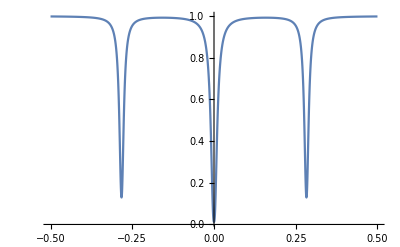

```mathematica
Plot[T/.rnum, {Δ, -.5, .5},PlotRange->All]
```

#### 3 aneis valores experimentais (unidades em GHz)

```mathematica
J=10/(√2); κe =3.6966659212142403;κi = 1.6586285453771623; κ = κi+κe;
```

```mathematica
(*J=10/(√2); κi =3.6966659212142403;κe = 1.6586285453771623; κ = κi+κe;*)
```

```mathematica
Ω=({{Δ+δ1, J, 0}, {J, Δ+δ2, J}, {0, J, Δ+δ3}}); a=({{a0}, {a1}, {a2}}); K=({{I √κe, 0, 0}}); Γ = Γi + Γe; Γi = ({{κi/2, 0, 0}, {0, κi/2, 0}, {0, 0, κi/2}}); Γe = ({{κe/2, 0, 0}, {0, 0, 0}, {0, 0, 0}});Cmatrix=1;
```

```mathematica
dadt = (I Ω - Γ).a + Transpose[K] sin//MatrixForm
```

(5 ⅈ √2 a1+(0.+1.92267 ⅈ) sin+a0 (-2.67765+ⅈ (Δ+δ1))
5 ⅈ √2 a0+5 ⅈ √2 a2+a1 (-0.829314+ⅈ (Δ+δ2))
5 ⅈ √2 a1+a2 (-0.829314+ⅈ (Δ+δ3)))

```mathematica
Solve[dadt[[1,1]]==0 && dadt[[1,2]]==0&& dadt[[1,3]]==0 , {a0,a1,a2}];
```

```mathematica
sout = Cmatrix sin+ K .a/.%
```

{{{sin-((0.+1.92267 ⅈ) ((0.+0. ⅈ)-(0.+1.92267 ⅈ) sin (-50.-1. (-0.829314+(0.+1. ⅈ) (Δ+δ2)) (-0.829314+(0.+1. ⅈ) (Δ+δ3)))))/(50. (-0.829314+(0.+1. ⅈ) (Δ+δ3))-1. (-2.67765+(0.+1. ⅈ) (Δ+δ1)) (-50.-1. (-0.829314+(0.+1. ⅈ) (Δ+δ2)) (-0.829314+(0.+1. ⅈ) (Δ+δ3))))}}}

```mathematica
t =sout/sin;
```

```mathematica
T =(t*Conjugate[t])^2//Simplify;
```

```mathematica
(*rnum={sin->1,δ->n×κ};*)
Manipulate[Plot[T/.{sin->1,δ1->m×κ,δ2->n×κ,δ3->p×κ}//Evaluate, {Δ, -50, 50},PlotRange->{All,{0,1}}],{m,-3,3},{n,-3,3},{p,-3,3}]
```

#### 3 aneis modified

```mathematica
a1=({{1}, {0}, {0}}); a2=({{0}, {1}, {0}}); a3=({{0}, {0}, {1}});
Ω=({{ω0, κ, 0}, {κ, ω0, κ}, {0, κ, ω0}});
```

```mathematica
Eigenvectors[Ω]
```

{{-1,0,1},{1,-√2,1},{1,√2,1}}

```mathematica
b1=({{1}, {-√2}, {1}});b2=({{-1}, {0}, {1}}); b3=({{1}, {√2}, {1}});
```

```mathematica
K=({{I μ1, 0, 0}});
```

```mathematica
S=({{1, -1, 1}, {-√2, 0, √2}, {1, 1, 1}});
```

```mathematica
Kb = K.Transpose[Inverse[S]]//MatrixForm//Simplify
```

((ⅈ μ1)/4 | -(ⅈ μ1)/2 | (ⅈ μ1)/4)

```mathematica
Γ = Γi + Γe; Γi = ({{γ, 0, 0}, {0, γ, 0}, {0, 0, γ}}); Γe = ({{μ1^2/2, 0, 0}, {0, 0, 0}, {0, 0, 0}}); Γb = Γ.Transpose[Inverse[S]]//MatrixForm//Simplify
```

(1/8 (2 γ+μ1^2) | 1/4 (-2 γ-μ1^2) | 1/8 (2 γ+μ1^2)
-γ/(2 √2) | 0 | γ/(2 √2)
γ/4 | γ/2 | γ/4)

#### 2 aneis

```mathematica
Ω=({{Δ, κ}, {κ, Δ}}); a=({{a0}, {a1}});K=({{I μ, 0}});Γ = Γi + Γe;Γi = ({{μ^2/2, 0}, {0, μ^2/2}});Γe = ({{μ^2/2, 0}, {0, 0}});sin=(sin1);Cmatrix=(1);
```

```mathematica
dadt = (I Ω - Γ).a + Transpose[K]sin//MatrixForm//Simplify
```

(ⅈ (a1 κ+sin1 μ+a0 (Δ+ⅈ μ^2))
ⅈ a1 Δ+ⅈ a0 κ-(a1 μ^2)/2)

```mathematica
Solve[dadt[[1,1]]==0 && dadt[[1,2]]==0, {a0,a1}]
```

{{a0→(ⅈ sin1 μ (-2 ⅈ Δ+μ^2))/(-2 Δ^2+2 κ^2-3 ⅈ Δ μ^2+μ^4),a1→-(2 sin1 κ μ)/(-2 Δ^2+2 κ^2-3 ⅈ Δ μ^2+μ^4)}}

```mathematica
sout = Cmatrix×sin+ K.a/.{a0->(ⅈ sin1 μ (-2 ⅈ Δ+μ^2))/(-2 Δ^2+2 κ^2-3 ⅈ Δ μ^2+μ^4),a1->-(2 sin1 κ μ)/(-2 Δ^2+2 κ^2-3 ⅈ Δ μ^2+μ^4)}//Simplify
```

{{sin1-(sin1 μ^2 (-2 ⅈ Δ+μ^2))/(-2 Δ^2+2 κ^2-3 ⅈ Δ μ^2+μ^4)}}

```mathematica
t =sout/sin1
T =(t*Conjugate[t])^2//Simplify
```

{{(sin1-(sin1 μ^2 (-2 ⅈ Δ+μ^2))/(-2 Δ^2+2 κ^2-3 ⅈ Δ μ^2+μ^4))/sin1}}

{{((2 Δ^2-2 κ^2+ⅈ Δ μ^2)^2 Conjugate[sin1-(sin1 μ^2 (-2 ⅈ Δ+μ^2))/(-2 Δ^2+2 κ^2-3 ⅈ Δ μ^2+μ^4)]^2)/((-2 Δ^2+2 κ^2-3 ⅈ Δ μ^2+μ^4)^2 Conjugate[sin1]^2)}}

```mathematica
rnum={μ->.1, κ->.2, sin->1};
```

```mathematica
T/.rnum
```

{{((-0.08+(0.+0.01 ⅈ) Δ+2 Δ^2)^2 (1-(0.01 (0.01+2 ⅈ Conjugate[Δ]))/(0.0801+(0.+0.03 ⅈ) Conjugate[Δ]-2 Conjugate[Δ]^2))^2)/((0.0801-(0.+0.03 ⅈ) Δ-2 Δ^2)^2)}}

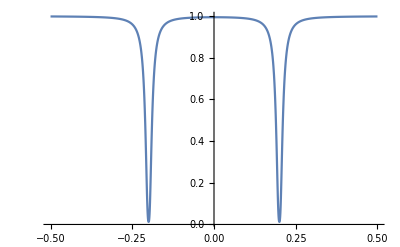

```mathematica
Plot[T/.rnum, {Δ, -.5, .5},PlotRange->All]
```

```mathematica
sout/.rnum
```

{{-ⅇ^(ⅈ θ)}}

#### 1 anel

```mathematica
Ω= Δ; a=a0;K=I μ;Γ = Γi + Γe; Γe =μ^2/2; Γi =μ^2/2;Cmatrix=1;
```

```mathematica
dadt = (I Ω - Γ)a + K sin//Simplify
```

ⅈ (sin μ+a0 (Δ+ⅈ μ^2))

```mathematica
Solve[dadt==0 , a0]
```

{{a0→(-sin Δ μ+ⅈ sin μ^3)/(Δ^2+μ^4)}}

```mathematica
sout = Cmatrix sin+ K a/.{a0->(-sin Δ μ+ⅈ sin μ^3)/(Δ^2+μ^4)}//Simplify
```

(sin Δ)/(Δ+ⅈ μ^2)

```mathematica
t =sout/sin
```

Δ/(Δ+ⅈ μ^2)

```mathematica
T =(t*Conjugate[t])^2//Simplify
```

(Δ^2 Conjugate[Δ]^2)/((Δ+ⅈ μ^2)^2 (Conjugate[Δ]-ⅈ Conjugate[μ]^2)^2)

```mathematica
T/.{μ->.1, κ->1, s->1}
```

(Δ^2 Conjugate[Δ]^2)/(((0.+0.01 ⅈ)+Δ)^2 ((0.-0.01 ⅈ)+Conjugate[Δ])^2)

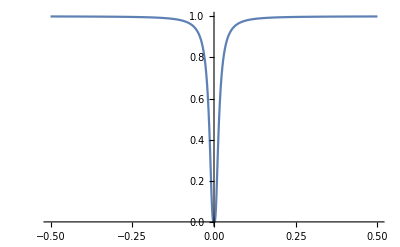

```mathematica
rnum={μ->.1, κ->1, s->1};
Plot[T/.rnum//Evaluate, {Δ, -.5, .5},PlotRange->All]
```